```mathematica
v1=1/Sqrt[3]{{0},{1},{1},{1}};
V1=KroneckerProduct[v1,ConjugateTranspose[v1]];
v2=1/Sqrt[3]{{0},{1},{Exp[I*2Pi/3]},{Exp[I*4Pi/3]}};
V2=KroneckerProduct[v2,ConjugateTranspose[v2]];
v3=1/Sqrt[3]{{0},{1},{Exp[I*4Pi/3]},{Exp[I*8Pi/3]}};
V3=KroneckerProduct[v3,ConjugateTranspose[v3]];
V4={{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
```

```mathematica
Phi00=1/2{{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}};
Phi01=1/2{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,0}};
Phi10=1/2{{1,0,0,-1},{0,0,0,0},{0,0,0,0},{-1,0,0,1}};
Phi11=1/2{{0,0,0,0},{0,1,-1,0},{0,-1,1,0},{0,0,0,0}};
```

```mathematica
E0=Sqrt[p]{{1,0},{0,Sqrt[1-t]}};
E1=Sqrt[p]{{0,0},{Sqrt[t],0}};
E2=Sqrt[1-p]{{Sqrt[1-t],0},{0,1}};
E3=Sqrt[1-p]{{0,Sqrt[t]},{0,0}};
```

```mathematica
M0=KroneckerProduct[E0,E0];
M1=KroneckerProduct[E0,E1];
M2=KroneckerProduct[E0,E2];
M3=KroneckerProduct[E0,E3];
M4=KroneckerProduct[E1,E0];
M5=KroneckerProduct[E1,E1];
M6=KroneckerProduct[E1,E2];
M7=KroneckerProduct[E1,E3];
M8=KroneckerProduct[E2,E0];
M9=KroneckerProduct[E2,E1];
M10=KroneckerProduct[E2,E2];
M11=KroneckerProduct[E2,E3];
M12=KroneckerProduct[E3,E0];
M13=KroneckerProduct[E3,E1];
M14=KroneckerProduct[E3,E2];
M15=KroneckerProduct[E3,E3];
```

```mathematica
Ch[X_]:=M0.X.Transpose[M0]+M1.X.Transpose[M1]+M2.X.Transpose[M2]+M3.X.Transpose[M3]+M4.X.Transpose[M4]+M5.X.Transpose[M5]+M6.X.Transpose[M6]+M7.X.Transpose[M7]+M8.X.Transpose[M8]+M9.X.Transpose[M9]+M10.X.Transpose[M10]+M11.X.Transpose[M11]+M12.X.Transpose[M12]+M13.X.Transpose[M13]+M14.X.Transpose[M14]+M15.X.Transpose[M15]
```

```mathematica
Clear[p,t]
```

```mathematica
Simplify[Ch[V1]+Ch[V2]+Ch[V3]+Ch[V4]]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

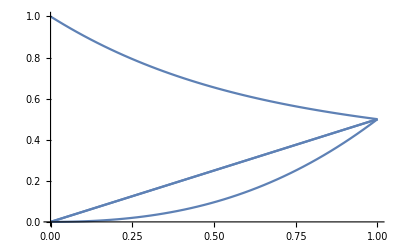

```mathematica
Plot[Simplify[Eigenvalues[Ch[Phi00]]],{t,0,1}]
```

```mathematica
t=.6;
```

```mathematica
FullSimplify[Eigenvalues[Ch[Phi00]]]
```

{t/2+(-1+p) p t^2,t/2+(-1+p) p t^2,1/2 (1+t (-1+t+2 (-1+p) p t)-√((-1+t)^2 (1+(1-2 p)^2 t^2))),1/2 (1+t (-1+t+2 (-1+p) p t)+√((-1+t)^2 (1+(1-2 p)^2 t^2)))}

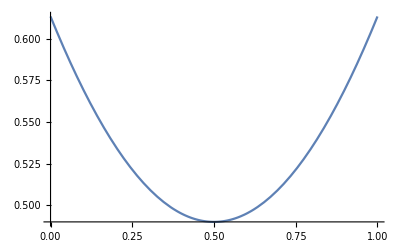

```mathematica
t=.6;
Plot[1/2 (1+t (-1+t+2 (-1+p) p t)+√((-1+t)^2 (1+(1-2 p)^2 t^2))),{p,0,1}]
```

```mathematica
FullSimplify[N[Eigenvalues[Ch[V3]]]]
```

{0.995565,0.00772978,0.00333333,4.81281×10^-6}

```mathematica
FullSimplify[N[Eigenvalues[Ch[V4]]]]
```

{0.9801,0.,0.,0.}

```mathematica
(1+Sqrt[1-t])^2
```

2.66491

```mathematica
FullSimplify[N[Eigenvalues[Ch[V2]]]]
```

```mathematica
FullSimplify[N[Eigenvalues[Ch[V1]]]]
```

```mathematica
Simplify[Eigenvalues[Ch[Phi10]]]
```

{t/2,t/2,1/2 (1-t+t^2-√((-1+t)^2 (1+t^2))),1/2 (1-t+t^2+√((-1+t)^2 (1+t^2)))}

```mathematica
Simplify[Eigenvalues[Ch[Phi11]]]
```

{1-t,0,0,-(-1+t) t}

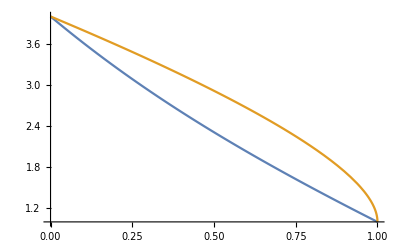

```mathematica
Plot[{2(1-t)+1-t+t^2+√((-1+t)^2 (1+t^2)),(1+Sqrt[1-t])^2},{t,0,1}]
```